# Nye/Berry Wavefront Dislocations

## 1 Dimensional Case

### Wave Pulse

```mathematica
G[t_, A_, B_, ω_]=A*Exp[1/B * -t^2]*Cos[-ω*t]
```

A ⅇ^(-t^2/B) Cos[t ω]

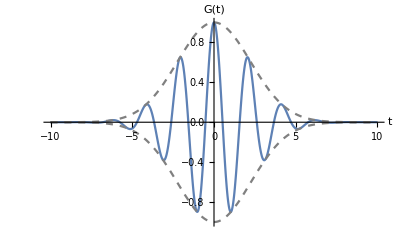

```mathematica
Show[
Plot[G[t, 1, 10, 3],{t, -10, 10}, AxesLabel -> {"t", "G(t)"}, PlotRange -> {{-10, 10}, {-1, 1}}],
Plot[G[t, 1, 10, 0], {t, -10, 10}, PlotStyle -> {Gray, Dashed}],
Plot[-G[t, 1, 10, 0], {t, -10, 10}, PlotStyle -> {Gray, Dashed}]
]
```

Interference of Two Pulses

```mathematica
TwoWaves[t_, d_] = G[t - d, 1, 10, 3] + G[t + d, 1, 10, 3]
```

ⅇ^(-1/10 (-d+t)^2) Cos[3 (-d+t)]+ⅇ^(-1/10 (d+t)^2) Cos[3 (d+t)]

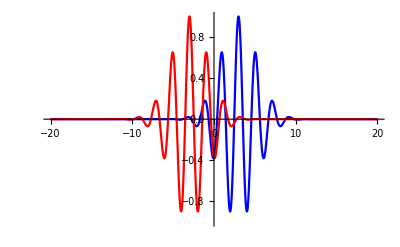

```mathematica
Show[
Plot[G[t - 3, 1, 10, 3], {t, -20, 20}, PlotStyle->Blue, PlotRange->{{-20, 20},{-1, 1}}],
Plot[G[t + 3, 1, 10, 3], {t, -20, 20}, PlotStyle -> Red, PlotRange->{{-20, 20},{-1, 1}}]
]
```

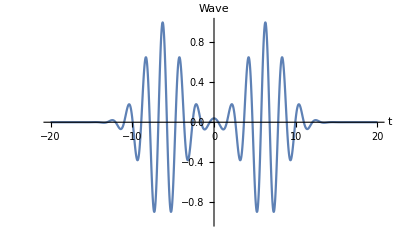

```mathematica
Plot[TwoWaves[t, (2*Pi*3)/(3*1)], {t, -20, 20}, AxesLabel -> {"t", "Wave"}, PlotRange -> {{-20, 20}, {-1, 1}}]
```

## 2D Case

### Plane wave

```mathematica
Pl1[x_, z_, t_, k1_, k3_, ω_, A_, B_] := A * (1 - B *(k1 * x + k3 * z - ω * t)) * Exp[I * (k1*x + k3*z -ω*t - 1/2 * Pi)]
```

```mathematica
Pl2[x_, z_, t_, k1_, k3_, ω_, A_, B_] := A * (1 + B *(-k1 * x + k3 * z - ω * t)) * Exp[I * (-k1*x + k3*z -ω*t + 1/2 * Pi)]
```

```mathematica
k=2
```

2

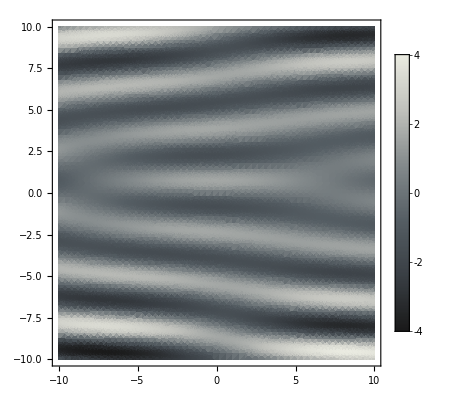

```mathematica
DensityPlot[Re[Pl1[x, z, 0, k*Sin[0.1], k*Cos[0.1], 3, 1, 0.1] + Pl2[x, z, 1, k*Sin[0.1], k*Cos[0.1], 3, 1, 0.1]], {x, -10, 10}, {z, -10, 10},PlotRange->All,PlotPoints->50,ColorFunction->"GrayTones",PlotLegends->Automatic]
```